## Pregunta 1

```mathematica
(1.a)
```

```mathematica
Sum[1/n^2,{n,1,Infinity}]
```

π^2/6

### (1.b)

```mathematica
Sum[1/n^4,{n,1,Infinity}]
```

π^4/90

```mathematica
1/2(4/3^2)^2
```

8/81

```mathematica
N[8/81]
```

0.0987654

## Pregunta 2

```mathematica
(A^2 Integrate[1/(9+w^2),{w,3,Infinity}])/Integrate[1/(9+w^2),{w,0,Infinity}]
```

A^2/2

## Pregunta 3

```mathematica
Integrate[Exp[t]Cos[ n t],t]
```

(ⅇ^t (Cos[n t]+n Sin[n t]))/(1+n^2)

```mathematica
Integrate[Exp[t]Sin[ n t],t]
```

(ⅇ^t (-n Cos[n t]+Sin[n t]))/(1+n^2)

```mathematica
a02=1/(2Pi)Integrate[Exp[t],{t,-Pi,Pi}]
```

(-ⅇ^-π+ⅇ^π)/(2 π)

```mathematica
an=Simplify[2/(2Pi)Integrate[Exp[t]Cos[n t],{t,-Pi,Pi}],Element[n,Integers]]
```

(2 (-1)^n Sinh[π])/(π+n^2 π)

```mathematica
bn=Simplify[2/(2Pi)Integrate[Exp[t]Sin[n t],{t,-Pi,Pi}],Element[n,Integers]]
```

-(2 (-1)^n n Sinh[π])/(π+n^2 π)

```mathematica
plot2a = Plot[Exp[t](UnitStep[t+Pi]-UnitStep[t-Pi]),{t,-3Pi,3Pi},PlotStyle->{Orange,Thickness[0.008]},PlotRange->All];
```

```mathematica
plot2b= Plot[1/Pi Sinh[Pi]+Sum[(2 (-1)^n Sinh[π])/(π+n^2 π)Cos[n t]-(2 (-1)^n n Sinh[π])/(π+n^2 π)Sin[n t],{n,1,100}],{t,-3Pi,3Pi},PlotStyle->{Blue,Thickness[0.01]},PlotRange->All];
```

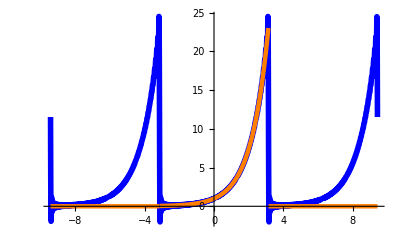

```mathematica
Show[plot2b,plot2a]
```

### (3.b)

```mathematica
Sum[1/(1+n^2),{n,1,Infinity}]
```

1/2 (-1+π Coth[π])

## Pregunta 4

```mathematica
(*Experimentemos un toque, obtengamos la inversa*)
```

```mathematica
InverseFourierTransform[(2 Exp[-I w])/(1+2 w^2),w,t,FourierParameters->{1,-1}]
```

ⅇ^(-Abs[-1+t]/(√2))/(√2)

```mathematica
(*Desplazemos como indica la funcion*)
```

```mathematica
ⅇ^(-Abs[-1+t]/(√2))/(√2)/.t->3t-5
```

ⅇ^(-Abs[-6+3 t]/(√2))/(√2)

```mathematica
(*Saquemole la transformada a eso*)
```

```mathematica
FourierTransform[ⅇ^(-Abs[-6+3 t]/(√2))/(√2),t,w,FourierParameters->{1, -1}]
```

(6 ⅇ^(-2 ⅈ w))/(9+2 w^2)

```mathematica
(*Da lo mismo*)
```

## Pregunta 5

```mathematica
a02 =1/T Integrate[A Cos[Pi/T t],{t,-T/2,T/2}]
```

(2 A)/π

```mathematica
an=Simplify[2/T Integrate[A Cos[Pi/T t]Cos[(2n Pi t)/T],{t,-T/2,T/2}],Element[n,Integers]]
```

(4 (-1)^n A)/(π-4 n^2 π)

```mathematica
bn =Simplify[2/T Integrate[A Cos[Pi/T t]Sin[(2n Pi t)/T],{t,-T/2,T/2}],Element[n,Integers]]
```

0